# Straightening at a Scale

A germ is a short shortest path, here of three edges ending at the centre of the graph. We extend it forward by k steps.

A walk is a geodesic at infra-scale r when every r+1 consecutive vertices of it form a shortest path. The observer checks straightness only within a horizon of r steps; at scale ∞ the whole walk is a shortest path.

The beam of the germ at scale r is the set of all geodesics at scale r that extend the germ by k steps. Its vertex density ρ(v) counts the visits of its members to v, and its edge density counts the traversals of an edge. A most visited member is one that maximizes the sum of the vertex and edge densities along it.

The question: from which scale r^* on is the most visited member of the beam a segment, a shortest path between its ends? We answer it on three lattices.

The beam is never listed. The geodesics at scale r through the germ are the walks of the window graph: a vertex is a window, the last r vertices of a walk, and an arrow appends one admissible step. The members of the beam are the walks of k edges from the germ's window, so the densities and the most visited members are read off powers of its adjacency matrix.

The pictures keep the embedding of the substrate so that the reader sees the plane; only the chord deviation below uses it.

## Setup

```mathematica
Needs["WolframInstitute`InfraGeometry`"]
```

The germ: a shortest path from the first vertex of the shell of radius 3 about the centre to the centre.

```mathematica
germ[g_] := With[{c = InfraCenter[g]}, First @ FindInfraRepresentative[g, InfraSegment[First @ FindInfraShell[g, c, 3], c], 1]]
```

The beam of k steps at scale r. With A the adjacency matrix of the window graph and e the indicator of the germ's window, the forward counts f_i=e A^i count the members that reach a window after i steps, and the backward counts b_i=A^(k-i)1 count the ways to finish from it.

```mathematica
beam[g_, germWalk_, r_, k_] := With[
  {windows = InfraMeasurement[g, InfraGeodesic[germWalk, r], "Graph"]},
  {a = AdjacencyMatrix[windows]},
  {from = UnitVector[VertexCount[windows], VertexIndex[windows, Take[germWalk, -Min[r, Length[germWalk]]]]]},
  <|"Germ" -> germWalk, "Windows" -> windows,
    "Forward" -> NestList[# . a &, from, k],
    "Backward" -> Reverse @ NestList[a . # &, ConstantArray[1, VertexCount[windows]], k]|>]
```

The vertex density: ρ(v)=∑_(i=0)^k ∑_w f_i(w) b_i(w) over the windows w ending at v; every member runs through the earlier vertices of the germ.

```mathematica
beamDensity[beam_] := Select[Positive] @ Merge[{
    Counts[Most @ beam["Germ"]] Total[Last @ beam["Forward"]],
    Merge[Thread[(Last /@ VertexList[beam["Windows"]]) -> Total[beam["Forward"] beam["Backward"]]], Total]},
  Total]
```

The endpoints, each with the number of members ending there: f_k on the windows ending at a vertex.

```mathematica
beamEndpoints[beam_] := Select[Positive] @ Merge[Thread[(Last /@ VertexList[beam["Windows"]]) -> Last[beam["Forward"]]], Total]
```

The edge density: ϵ(uv)=∑_(i=0)^(k-1) ∑f_i(w) b_(i+1)(w') over the arrows w→w' of the window graph stepping between u and v.

```mathematica
beamEdgeDensity[beam_] := With[
  {tips = Last /@ VertexList[beam["Windows"]], steps = AdjacencyMatrix[beam["Windows"]]["NonzeroPositions"]},
  Select[Positive] @ Merge[{
      Counts[Sort /@ Partition[beam["Germ"], 2, 1]] Total[Last @ beam["Forward"]],
      Merge[Thread[(Sort /@ Map[tips[[#]] &, steps]) ->
        Total @ MapThread[#1[[steps[[All, 1]]]] #2[[steps[[All, 2]]]] &, {Most @ beam["Forward"], Rest @ beam["Backward"]}]], Total]},
    Total]]
```

The most visited members: a longest path through the layers 0,…,k of the window graph, each step weighted by ρ of the vertex it reaches and ϵ of the edge it uses. The window determines the walk, so every maximal chain of windows is one most visited member, and all ties are kept.

```mathematica
mostVisited[beam_] := With[
  {tips = Last /@ VertexList[beam["Windows"]], steps = AdjacencyMatrix[beam["Windows"]]["NonzeroPositions"],
   rho = beamDensity[beam], eps = beamEdgeDensity[beam], fw = beam["Forward"], bw = beam["Backward"]},
  {layers = Table[
    With[{live = Pick[steps, Sign[fw[[i, steps[[All, 1]]]] bw[[i + 1, steps[[All, 2]]]]], 1]},
      Thread[live -> Lookup[rho, tips[[live[[All, 2]]]]] + Lookup[eps, Key /@ Sort /@ Map[tips[[#]] &, live]]]],
    {i, Length[fw] - 1}]},
  {best = FoldList[{score, layer} |-> GroupBy[layer, #[[1, 2]] & -> (score[#[[1, 1]]] + #[[2]] &), Max],
    <|First @ Ordering[First @ fw, -1] -> 0|>, layers]},
  {tight = Graph @ Catenate @ Table[
    DirectedEdge[{i - 1, #[[1, 1]]}, {i, #[[1, 2]]}] & /@
      Select[layers[[i]], best[[i, Key @ #[[1, 1]]]] + #[[2]] == best[[i + 1, Key @ #[[1, 2]]]] &],
    {i, Length[layers]}]},
  Join[beam["Germ"], tips[[#[[2 ;;, 2]]]]] & /@ Catenate @ Map[
    FindPath[tight, {0, First @ Keys @ First @ best}, {Length[layers], #}, Infinity, All] &,
    Keys @ MaximalBy[Last @ best, Identity]]]
```

The chord deviation of a walk: the largest distance of its vertices from the chord joining its ends, in units of the edge length. It is the one readout that uses the embedding.

```mathematica
deviation[g_, walk_] := With[
  {xy = AssociationThread[VertexList[g], GraphEmbedding[g]]},
  {unit = Mean[EuclideanDistance @@ Lookup[xy, List @@ #] & /@ EdgeList[g]]},
  Max[RegionDistance[Line[Lookup[xy, {First @ walk, Last @ walk}]], #] & /@ Lookup[xy, walk]] / unit]
```

## The beam at a scale

Each picture is one lattice at one scale: the rows are the square, the triangular and the hexagonal tiling, the columns the scales r=2,4,8. The beam extends the germ by ten steps.

The vertex density of the beam is orange, its endpoints green, each sized by the number of members ending there. The most visited members are red, all of them; the germ is drawn last.

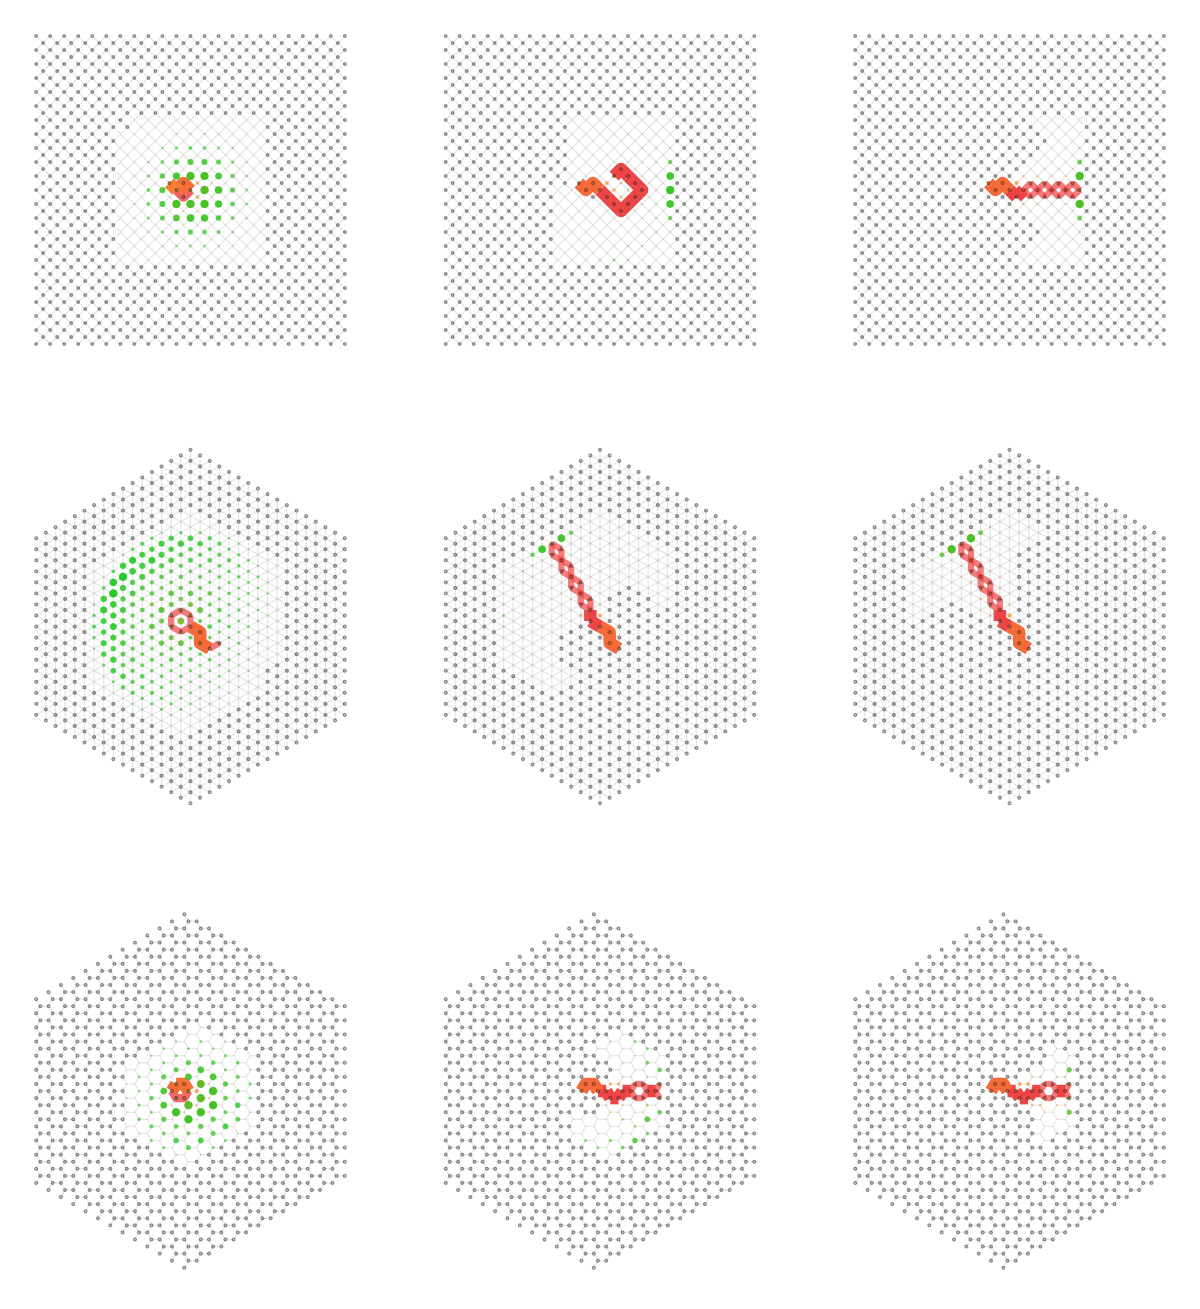

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, "Large", "KeepCoordinates" -> True])},
    {germWalk = germ[g]},
    {b = beam[g, germWalk, r, 10]},
    InfraSubstrateHighlight[g,
      {beamDensity[b] -> StandardOrange, beamEndpoints[b] -> StandardGreen, InfraWalk /@ mostVisited[b] -> StandardRed, InfraWalk[germWalk] -> StandardOrange}]],
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph"}},
  {r, {2, 4, 8}}]
```

At the smallest scale the beam fans out over a wide region and its endpoints fill it. Every member starts at the germ, so the density is highest there, and the most visited member is the one that stays near the germ: it circles around the centre. A geodesic at a small scale may revisit a vertex, and these members do.

From a scale on the endpoints gather on a short arc and the most visited members run straight away from the germ. On the square tiling this happens later than on the other two: at the middle scale its most visited member still bends away.

The straight members do not continue the germ's direction. On the square tiling they run along the diagonal of the cone of the two lattice directions that contains the germ: a lattice keeps a direction only up to its cone.

## The scale of straightness

Three readouts of the most visited members, for every scale r=2,…,10, each the worst over the ties. The extension is a member without the germ.

The excess of an extension is its length minus the distance between its ends. It is zero exactly when the extension is a segment, so the threshold r^* is the scale where the excess first vanishes.

The chord deviation is read in the plane; the spread of the endpoints is the largest distance between two of them.

```mathematica
readouts = Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, "Large", "KeepCoordinates" -> True])},
    {germWalk = germ[g], d = GraphDistanceMatrix[g]},
    Table[
      With[
        {b = beam[g, germWalk, r, 10]},
        {walks = Drop[#, Length[germWalk] - 1] & /@ mostVisited[b], ends = VertexIndex[g, #] & /@ Keys[beamEndpoints[b]]},
        {r, Max[Length[#] - 1 - d[[VertexIndex[g, First @ #], VertexIndex[g, Last @ #]]] & /@ walks], Max[deviation[g, #] & /@ walks], Max[d[[ends, ends]]]}],
      {r, 2, 10}]],
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph"}}];
```

The excess against the scale.

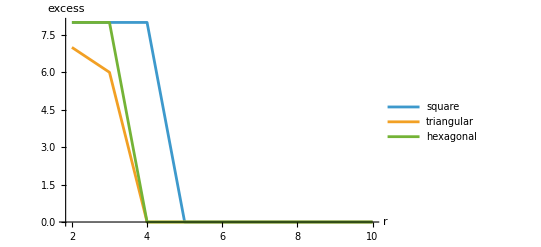

```mathematica
ListLinePlot[readouts[[All, All, {1, 2}]],
  PlotRange -> All, AxesLabel -> {Text["r"], Text["excess"]},
  PlotLegends -> Text /@ {"square", "triangular", "hexagonal"}]
```

Below the threshold the most visited extension is far from a segment; at the threshold the excess drops to zero in one step and stays there. The most visited member jumps from a walk near the germ to a segment.

The triangular and the hexagonal tilings share the threshold; the square tiling reaches it one scale later.

The chord deviation against the scale.

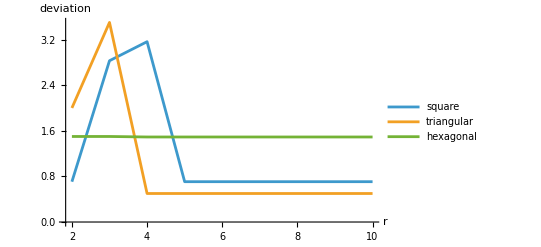

```mathematica
ListLinePlot[readouts[[All, All, {1, 3}]],
  PlotRange -> All, AxesLabel -> {Text["r"], Text["deviation"]},
  PlotLegends -> Text /@ {"square", "triangular", "hexagonal"}]
```

On the square and the triangular tilings the deviation falls at the same threshold to a floor, the staircase of a segment off the lattice directions.

The deviation is blind to a closed loop: a member that circles a face stays close to its short chord. On the hexagonal tiling it does not see the threshold at all, since a straight extension zigzags as far from its chord as a bent one.

The spread of the endpoints against the scale.

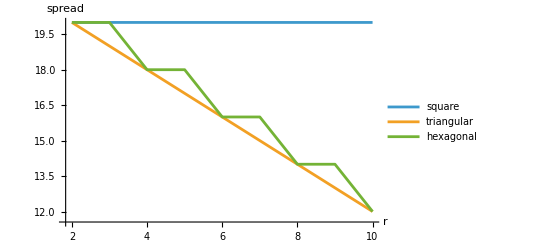

```mathematica
ListLinePlot[readouts[[All, All, {1, 4}]],
  PlotRange -> All, AxesLabel -> {Text["r"], Text["spread"]},
  PlotLegends -> Text /@ {"square", "triangular", "hexagonal"}]
```

On the triangular and the hexagonal tilings the endpoints keep gathering past the threshold: the straightening of the most visited member comes first, the narrowing of the beam later.

On the square tiling the spread never falls. At a large scale the beam fills the cone of two lattice directions, and its endpoints lie on one antidiagonal, all at the same distance from the germ: the path metric of the square lattice is the ℓ^1 metric.

## Open questions

[[ The inextensible geodesic at scale r as an object: the infinite walks of the window graph from the germ's window. Is its most visited member eventually a ray at every scale above r^*, and how does r^* depend on the length of the germ? ]]

[[ The loss of direction on a lattice: the straight members follow the cone, not the germ. Does a mesh or a sprinkling, with no preferred directions, restore the germ's direction at large scales? ]]

Related Guides

EuclideanInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/EuclideanInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/StraighteningAtScaleTutorial

### Keywords

geodesic

infra-scale

germ

extension

beam

window graph

most visited

straightness

segment

tiling